```mathematica
(* Parameters *)
l=3; g=4; Cc=2; h=1; n=0.74; m = (l+2*Cc)/2;
BL = g*(Cc+Tanh[n*l/2]/n);
BR = g*(l+2*Cc)-BL;
```

```mathematica
(* Piecewise function *)
pExact[x_] = Piecewise[{{-g*x+BL, x<Cc},{-g*Sinh[n*(x-m)]/(n*Cosh[n*l/2]),Cc<x<l+Cc}, {-g*x+g*(l+2*Cc)-BL,x>l+Cc}}]
```

Piecewise[{{12.3463-4 x, x<2}, {-3.21376 Sinh[0.74 (-7/2+x)], 2<x<5}, {15.6537-4 x, x>5}, {0, True}}]

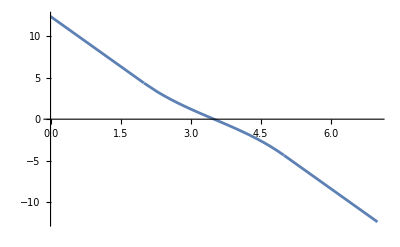

```mathematica
Plot[pExact[x],{x,0,l+2*Cc}]
```

```mathematica
pL[x_] = BL - 2*x*BL/(l+2*Cc);
```

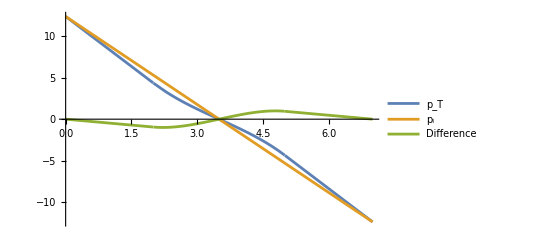

```mathematica
Plot[{pExact[x],pL[x],pExact[x]-pL[x]},{x,0,l+2*Cc},PlotLegends->{Times[Subscript["p","T"]],Times[Subscript["p","l"]],"Difference"}]
```

```mathematica
Clear[η,xm,G,bL,c,L]
pExactAnon[x_] = Piecewise[{{-G*x+bL, x<c},{-G*Sinh[η*(x-xm)]/(η*Cosh[η*L/2]),c<x<L+c}, {-G*x+G*(L+2*c)-bL,x>L+c}}]
```

Piecewise[{{bL-G x, x<c}, {-(G Sech[(L η)/2] Sinh[(x-xm) η])/η, c<x<c+L}, {-bL+G (2 c+L)-G x, x>c+L}, {0, True}}]

```mathematica
pLAnon[x_] = bL-2*x*bL/(L+2*c);
pDiff[x_] =pExactAnon[x]-pLAnon[x]
```

-bL+(2 bL x)/(2 c+L)+(Piecewise[{{bL-G x, x<c}, {-(G Sech[(L η)/2] Sinh[(x-xm) η])/η, c<x<c+L}, {-bL+G (2 c+L)-G x, x>c+L}, {0, True}}])

```mathematica
Simplify[pDiff[x]]
```

bL (-1+(2 x)/(2 c+L))+(Piecewise[{{bL-G x, x<c}, {-(G Sech[(L η)/2] Sinh[(x-xm) η])/η, c<x<c+L}, {-bL+G (2 c+L-x), x>c+L}, {0, True}}])

```mathematica
Integrate[bL-G*x,{x,0,c}]
```

bL c-(c^2 G)/2

```mathematica
Integrate[-(G Sech[(L η)/2] Sinh[(x-xm) η])/η,{x,c,L+c}]
```

(G (Cosh[(c-xm) η]-Cosh[(c+L-xm) η]) Sech[(L η)/2])/η^2

```mathematica
Integrate[-bL+G*(2*c+L-x),{x,L+c,L+2*c}]
```

-bL c+(c^2 G)/2